data的总长度: 5036

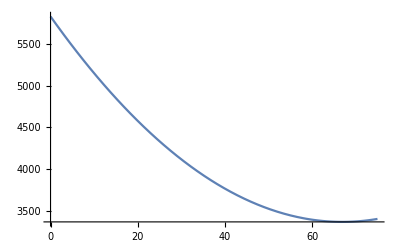

```mathematica
data=Import["C:\\Users\\18055\\Desktop\\Workdir\\src\\data2\\data2.csv","CSV"];
totallength=Length[data];
Print["data的总长度: ",totallength];
(*构建初始值关于年龄的datainitial*)
datainitial={};i=1;
While[i<=totallength,If[data[[i,4]]==0 ,AppendTo[datainitial,{data[[i,3]],10^data[[i,5]]-1}]];i++;];
modelini=a*x^2+b*x+c;
apporxini=FindFit[datainitial,{modelini},{a,b,c},x];
paramsini=modelini/.apporxini;(*paramsini就是初始值与年龄的预测函数*)
Plot[paramsini,{x,0,75}]
```

```mathematica
(*Define 治疗方式(1,2,3,4)  数据筛孔大小  待预测年龄*)(*返回参数表{a->_,b->_,c->_},其中a,b,c是方程a*x^2+b*x+c的参数*)
predict[type_,Minlength_,age_]:=Module[{datatype,i,datatypelength,datatypersonal,t,flag,datatypersonalength,DataTypeRealLength,model,paramsX,approx,params,sum2,sum3,length,const},
(*读取type的所有记录，记录在datatpye内*)
datatype={};
i=1;
While[i<=totallength,If[data[[i,2]]==type ,AppendTo[datatype,{data[[i,1]],data[[i,3]],data[[i,4]],10^data[[i,5]]-1}]];i++;];
datatypelength=Length[datatype];

(*构建个人信息矩阵表datatypersonal*)
datatypersonal={{datatype[[1,2]],{ {datatype[[1,3]],datatype[[1,4]]}} }};
i=2;
t=1;
flag=datatype[[1,1]];
While[i≤datatypelength,
If[datatype[[i,1]]==flag,AppendTo[datatypersonal[[t,2]],datatype[[i,{3,4}]]],AppendTo[datatypersonal,{datatype[[i,2]],{datatype[[i,{3,4}]]}}];flag=datatype[[i,1]];t++;];
i++;
];
datatypersonalength=Length[datatypersonal];

(*删除无效数据，更新datatypersonal*)
i=1;
While[i≤datatypersonalength,If[Length[datatypersonal[[i,2]]]≤Minlength,datatypersonal=Delete[datatypersonal,{i}];datatypersonalength--;,i++;]];
DataTypeRealLength=Length[datatypersonal];

(*预测个人结果：目的是得出a+b*x+c*x^2的b和c*)
model=a+b*x+c*x^2;i=1;
paramsX={};
While[i≤DataTypeRealLength,approx=FindFit[datatypersonal[[i,2]],{model},{a,b,c},x];
params={a,b,c}/.approx;
AppendTo[paramsX,params];i++;
];
length=Length[paramsX];
sum2=Sum[paramsX[[x,2]],{x,1,length}];
sum2=sum2/length;
sum3=Sum[paramsX[[x,3]],{x,1,length}];
sum3=sum3/length;

(*计算参数表的常数项*)
const=paramsini/.{x->age};
{a->sum3,b->sum2,c->const}
];
```

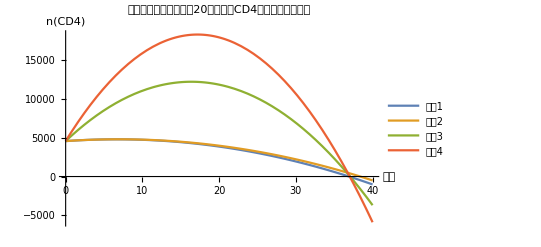

```mathematica
(*实际预测*)
age=20;(*设置待预测人的年龄*)
result={};
For[i=1,i≤4,i++,AppendTo[result,(a*x^2+b*x+c)/.predict[i,4,age]]];
Plot[result,{x,0,40},PlotLegends->{"疗法1","疗法2","疗法3","疗法4"},AxesLabel->{"周数","n(CD4)"},PlotLabel->"不同疗法下随周数变化" <>ToString[age]<>"岁人体内CD4数量的变化预测图"]
```

由图像可知，疗法4的效果最好，能大幅度提高CD4的浓度，有效缓解病情，其次是疗法3。疗法1、2 的效果都不是很理想，只能减缓病情恶化的速度